```mathematica
Exit[];
```

```mathematica
$Assumptions=  r>0 && Element[m,Integers] && Element[n,Integers]  && s>0 && Element[k,Integers] && k>0
```

r>0&&m∈Integers&&n∈Integers&&s>0&&k∈Integers&&k>0

# 2-d Dirac

```mathematica
f1[r_,En_]:={{(m-1)/r,I*(En-r^p)},{I*(En-r^p),-m/r}};f1[r,En]//MatrixForm
```

((-1+m)/r | ⅈ (En-r^p)
ⅈ (En-r^p) | -m/r)

# Diagonaldarstellung für r gegen Infinity

```mathematica
V={{1,1},{-1,1}};Simplify[V.f1[r,En].Inverse[V]]//MatrixForm
```

(ⅈ En-1/(2 r)-ⅈ r^p | (1-2 m)/(2 r)
(1-2 m)/(2 r) | -ⅈ En-1/(2 r)+ⅈ r^p)

```mathematica
Inverse[V].{0,C}
```

{-C/2,C/2}

# Potenzreihenansatz mit richtigem Rangverhalten

# m<=0

```mathematica
s=-m;p=2;
```

```mathematica
f1[r,En]//MatrixForm
```

((-1+m)/r | ⅈ (En-r^2)
ⅈ (En-r^2) | -m/r)

```mathematica
u={F[x],G[x]}*x^(s)
```

{x^-m F[x],x^-m G[x]}

```mathematica
r[x_]:=x;
```

```mathematica
g1=Collect[Expand[Simplify[Expand[-(D[u,x]-r'[x]*f1[r[x],En].u)/x^(s-0)]]],{x^n,a[n],b[n],F[x],G[x]}];
g1
```

{(-1/x+(2 m)/x) F[x]+(ⅈ En-ⅈ x^2) G[x]-F'[x],(ⅈ En-ⅈ x^2) F[x]-G'[x]}

```mathematica
f[r_,En_]:={{(-1/x+(2 m)/x) ,(ⅈ En-ⅈ x^p) },{(ⅈ En-ⅈ x^p),0}};f[r,En]//MatrixForm
```

(-1/x+(2 m)/x | ⅈ En-ⅈ x^2
ⅈ En-ⅈ x^2 | 0)

```mathematica
u={a[n],b[n]}*x^n*Exp[I*x^(p+1)/(p+1)]
```

{ⅇ^((ⅈ x^3)/3) x^n a[n],ⅇ^((ⅈ x^3)/3) x^n b[n]}

```mathematica
g1=Collect[Expand[Simplify[Expand[-(D[u,x]-r'[x]*f[r[x],En].u)*x/Exp[I*x^(p+1)/(p+1)]]]],{x^n,a[n],b[n],F[x],G[x]}];
g1
```

{x^n ((-1+2 m-n-ⅈ x^3) a[n]+(ⅈ En x-ⅈ x^3) b[n]),x^n ((ⅈ En x-ⅈ x^3) a[n]+(-n-ⅈ x^3) b[n])}

```mathematica
g2=Table[Simplify[Sum[D[g1,{x,n2}]/n2!,{n,0,10}]/.x->0],{n2,0,10}];g2//MatrixForm
```

(0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0)

```mathematica
a[0]=0;b[0]=1; b[1]=0 ;a[2]=0 ;a[1]=-ⅈ En/2 /(-1+m);b[2]=ⅈ En a[1]/2;
```

```mathematica
a[1]=.;a[2]=.;b[1]=.;b[0]=.;a[0]=.;b[2]=.;a[n_]=.;b[n_]=.
```

```mathematica
a[n_]:=I/(n+1-2 m)* (En b[n-1]-a[n-3]-b[n-3]);b[n_]:=1/n ⅈ (-a[n-3]+En a[n-1]-b[n-3])
```

```mathematica
Un[Ene_,mm_,nN_,x_]:=Module[{n,U1,U2,U3,U4,Erg},
U1={a[0],b[0]};U2={a[1],b[1]}/.m->mm/.En->Ene;U3={a[2],b[2]}/.m->mm/.En->Ene;
Erg=U1+U2*x+U3*x^2;
For[n=3,n≤nN,n++,
U4=Simplify[{I/(n+1-2 mm)* (Ene U3[[2]]-U1[[1]]-U1[[2]]),1/n ⅈ (Ene U3[[1]]-U1[[1]]-U1[[2]])}]//N;
U1=U2;U2=U3;U3=U4;
Erg+=U3*x^n;

];

Erg]
```

# zur Probe

```mathematica
Uno[Ene_,m_,nN_,x_]:=Module[{n,U,Erg=0},
U={{a[0],b[0]}};
For[n=1,n≤nN+1,n++,
AppendTo[U,{a[n],b[n]}]
];
For[n=0,n≤nN,n++,
Erg+=U[[n+1]]*x^n;
];
Erg
]
```

```mathematica
Simplify[Un[En,m,10,x]-Uno[En,m,10,x]]
```

{0,0}

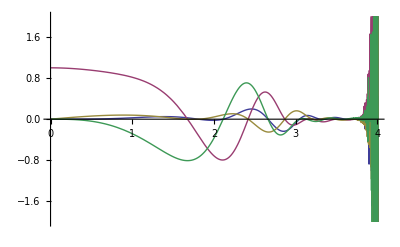

```mathematica
G={Re[#],Im[#]}&[Un[3,-10,350,x]];Plot[G,{x,0,4},PlotRange->{-2,2}]
```

```mathematica
U[En_,m_,g_,X_]:=Module[{n=10,U,G},
U=Un[En,m,n,X];G=-Un[En,m,n+1,X];
While[Sqrt[Abs[Conjugate[U-G].(U-G)]]>g,
n++;
U=G;G=-Un[En,m,n+1,X];

];
{Un[En,m,n,X],n}]
```

```mathematica
U[9,5,0.0001,1]
```

{{-0.0126898,0.+0.00407705 ⅈ},14}

```mathematica
Ener[Ene_]:=Module[{U1,U2,U1S,U2S,VV={{0,1},{-1,0}},En,Enn,NN,Erg,kE,k,n,m,r,h},
En=Ene;
Label[begin];
n=5000;
m=5;
r=7.2//N;h=-7.0/n;
k={1,-1};
kE={0,0};
Do[
k0=h*f[r,En].k;k1=h*f[r+h/2,En].(k+k0/2);k2=h*f[r+h/2,En].(k+k1/2);k3=h*f[r+h,En].(k+k2);
k+=1/6*(k0+2*k1+2*k2+k3);

k0=h*(fE.k+f[r,En].kE);k1=h*(fE.k+f[r+h/2,En].(kE+k0/2));k2=h*(fE.k+f[r+h/2,En].(kE+k1/2));k3=h*(fE.k+f[r+h,En].(kE+k2));
kE+=1/6*(k0+2*k1+2*k2+k3);

r+=h;
,{n}];

NN=U[En,m,0.0001,r][[2]];

{U1,U2}=Un[En,m,NN,r];
{U1S,U2S}=D[Un[Enn,m,NN,r],Enn]/.Enn->En;

Erg=k[[1]]*U2-U1*k[[2]];

If[Abs[Erg/U2/k[[2]]]>0.02,
En-=Erg/(U2S k⟦1⟧-U1S k⟦2⟧+U2 kE⟦1⟧-U1 kE⟦2⟧);
Print[{En,Erg/U2/k[[2]]}];Goto[begin];
 ];
{En,Erg/U2/k[[2]]}
]
```

```mathematica
For[i=0,i<10,i+=0.1,Sepp=Ener[i];Print[{i,Sepp}];AppendTo[Energie,{i,Sepp}];]
```

```mathematica
Ener[22]
```

{21.8924+0.168499 ⅈ,-0.262337+1.54006 ⅈ}

{21.7276+0.288878 ⅈ,0.0977574+1.99468 ⅈ}

{21.5078+0.261371 ⅈ,1.15369+1.40345 ⅈ}

{21.6825+0.0732421 ⅈ,0.410727+0.725268 ⅈ}

{21.6223+0.137127 ⅈ,-1.84205+0.583011 ⅈ}

{21.5895+0.1468 ⅈ,-0.181458-0.525624 ⅈ}

{21.5862+0.143899 ⅈ,0.0316819-0.0363388 ⅈ}

{21.5862+0.143899 ⅈ,0.000384958+0.000557679 ⅈ}

```mathematica
Energie={3.77486283903418+0.22786873407418717 ⅈ,
5.928479968617718+0.2815986526347655 ⅈ,
7.8813588488087065+0.30953294412328675 ⅈ,
7.881329304880588+0.3095336916562825 ⅈ,
9.71036454189739+0.3304415424573178 ⅈ,
11.458077781781169+0.3457848857997222 ⅈ,
13.139764183242892+0.3546744769440479 ⅈ,
13.139114444715846+0.3548172513559829 ⅈ,
14.76566063867228+0.3636637795053202 ⅈ,
16.34527139193304+0.3681521067888729 ⅈ,
17.892138695416435+0.3696213478944415 ⅈ,
19.40831608562361+0.37704222997528414 ⅈ,
20.886015743223094+0.38097023642873473 ⅈ,
22.34958939297449+0.38276309915136164 ⅈ,23.777494591007947+0.3872991704766671 ⅈ,12.207301904640477+0.09130244038237889 ⅈ,13.879319291317909+0.10359131716054014 ⅈ,17.071331521063737+0.12274708920757649 ⅈ,18.607651751873114+0.1305970820854307 ⅈ,20.11139546248976+0.1375815129955693 ⅈ,21.586240037178456+0.14389862151162078 ⅈ};Energie//MatrixForm
```

(3.77486+0.227869 ⅈ
5.92848+0.281599 ⅈ
7.88136+0.309533 ⅈ
7.88133+0.309534 ⅈ
9.71036+0.330442 ⅈ
11.4581+0.345785 ⅈ
13.1398+0.354674 ⅈ
13.1391+0.354817 ⅈ
14.7657+0.363664 ⅈ
16.3453+0.368152 ⅈ
17.8921+0.369621 ⅈ
19.4083+0.377042 ⅈ
20.886+0.38097 ⅈ
22.3496+0.382763 ⅈ
23.7775+0.387299 ⅈ
12.2073+0.0913024 ⅈ
13.8793+0.103591 ⅈ
17.0713+0.122747 ⅈ
18.6077+0.130597 ⅈ
20.1114+0.137582 ⅈ
21.5862+0.143899 ⅈ)

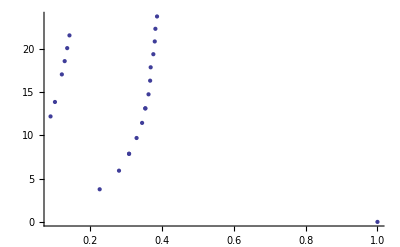

```mathematica
ListPlot[Append[{Im[#],Re[#]}&/@Energie,{1,0}],AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
:
```

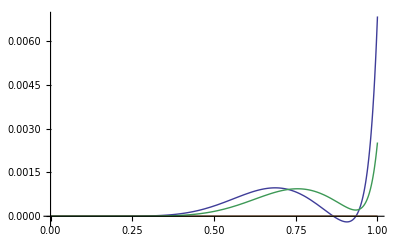

```mathematica
G={Re[#],Im[#]}&[Un[16,10,15,x]];Plot[G,{x,0,1},PlotRange->All]
```

27

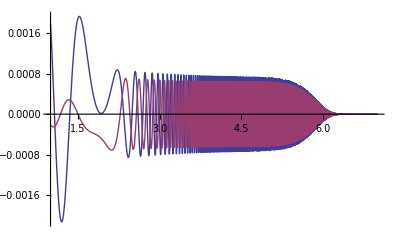

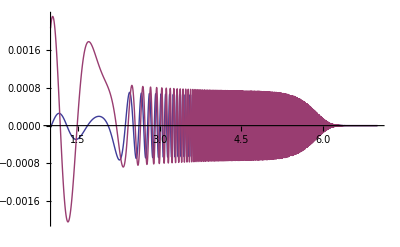

```mathematica
n=8000;S=1;h=6/n;ra=1;En=Energie[[17]];m=5;r=1;
U[En,m,10^-10,r][[2]]
k=U[En,m,10^-10,r][[1]];
kK={{r,k}};
Do[
k0=h*f[r,En].k;k1=h*f[r+h/2,En].(k+k0/2);k2=h*f[r+h/2,En].(k+k1/2);k3=h*f[r+h,En].(k+k2);
k+=1/6*(k0+2*k1+2*k2+k3);r+=h;
AppendTo[kK,{r,k}],{n}];

ListPlot[Join[{ {#[[1]],Re[#[[2,1]]]}&/@kK[[S;;n]]//N},{ {#[[1]],Im[#[[2,1]]]}&/@kK[[S;;n]]//N}],PlotRange->All,Joined->True]
ListPlot[Join[{ {#[[1]],Re[#[[2,2]]]}&/@kK[[S;;n]]//N},{ {#[[1]],Im[#[[2,2]]]}&/@kK[[S;;n]]//N}],PlotRange->All,Joined->True]
En=.;r=.;
```

```mathematica
U[En,m,10^-10,r][[1]]
```

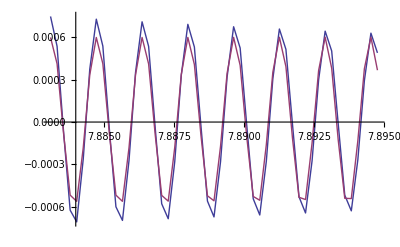

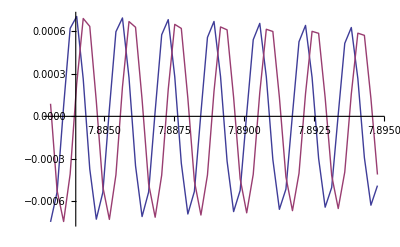

```mathematica
S=29500;n=50;ListPlot[Join[{ {#[[1]],Re[#[[2,1]]]}&/@kK[[S;;S+n]]//N},{ {#[[1]],-0.0006*Sin[#[[1]]^5/5+1-#[[1]]*Re[Energie[[11]]]]}&/@kK[[S;;S+n]]//N}],PlotRange->All,Joined->True]
ListPlot[Join[{ {#[[1]],Re[#[[2,2]]]}&/@kK[[S;;S+n]]//N},{ {#[[1]],Im[#[[2,2]]]}&/@kK[[S;;S+n]]//N}],PlotRange->All,Joined->True]
```

```mathematica
Exp[I*Im[Energie[[1]]]*x]
```

ⅇ^(0.278733 ⅈ x)